# UV derivatives with CFF

```mathematica
Quit[]
```

## Resources

```mathematica
SetAttributes[SP4,Orderless];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*<<FeynCalc`*)
```

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/cLTD.m"]
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/UV_derivatives_with_CFF/cLTD_work_dir/
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

## Simple dod=1 triangle

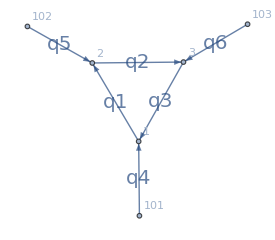

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,1,3],
DirectedEdge[101,1,4],DirectedEdge[102,2,5],DirectedEdge[103,3,6]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|1->1,2->2,3->3|>,lmb->{1}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
Tri1Lnumerics=GenerateRandomSample[Tri1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147}

```mathematica
GenerateLMBData[g_]:=Module[
{
edges=EdgeList[g],
props,
lmbEdgesIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetLMBEdges[g]}],
externals=cFFGetExternalEdges[g]
},
Association[Table[
props=(e/.DirectedEdge[_,_,props_]:>props);
props["id"]-><|
"mass"->props["mass"],
"lmb_decomposition"->(
props["sig"]⟦1⟧.Table[q[i],{i,Length[lmbEdgesIDs]}]
+props["sig"]⟦2⟧.Table[q[i+3],{i,Length[externals]}]
)
|>
,{e,edges}
]]
]
```

```mathematica
GetVirtualPropagators[g_]:=Module[
{
externalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[g]}]
},
Select[EdgeList[g],Not[MemberQ[externalIDs,(#/.DirectedEdge[_,_,props_]:>props)["id"]]]&]
]
```

```mathematica
GetVirtualPropagatorsIDs[g_]:=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,GetVirtualPropagators[g]}]
```

```mathematica
ExpandSP4[Num_]:=TensorExpand[Num/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]};
```

```mathematica
(*Tri1Lnumerator=SP4[q[1],q[2]]SP4[q[3],q[4]]+SP4[q[1],q[3]]SP4[q[2],q[5]]+SP4[q[1],q[2]]+SP4[q[1],q[3]]+1 ;*)
```

```mathematica
Tri1Lnumerator=SP4[q[1],q[2]]SP4[q[3],q[4]];
```

```mathematica
(*Tri1Lnumerator=SP4[q[1],q[3]]SP4[q[2],q[5]];*)
```

```mathematica
(*Tri1Lnumerator=SP4[q[1],q[2]];*)
```

```mathematica
Tri1LcLTDexpr=GeneratecLTDExpression[Tri1L,Num->Tri1Lnumerator];
Print["cLTD result: ",EvalcLTD[Tri1LcLTDexpr,Tri1Lnumerics]//N//FullForm];
Tri1LcFFexpr=CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Tri1L,Tri1LcFFexpr,Tri1Lnumerics,Num->Tri1Lnumerator,DEBUG->False]//N//FullForm];
```

cLTD result: Complex[0.,0.0027871]

cFF result : Complex[0.,0.0027871]

```mathematica
Tri1LPropagators=GenerateLMBData[Tri1L];
```

```mathematica
Tri1L4DExpr=Num[Tri1Lnumerator]/Times@@Table[1/λ^2 Denom[ie,SP4[q[ie][λ],q[ie][λ]]-λ^2 m[ie]^2+(m[ie]^2-mUV^2)],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
```

(λ^6 Num(SP4(q(1),q(2)) SP4(q(3),q(4))))/(Denom(1,SP4(q(1)(λ),q(1)(λ))-λ^2 (m(1))^2+(m(1))^2-mUV^2) Denom(2,SP4(q(2)(λ),q(2)(λ))-λ^2 (m(2))^2+(m(2))^2-mUV^2) Denom(3,SP4(q(3)(λ),q(3)(λ))-λ^2 (m(3))^2+(m(3))^2-mUV^2))

```mathematica
Tri1L4DExprWithFullLambdaDep=Collect[(1/λ)^4 Tri1L4DExpr/.
{
Num[x__]:>(x
/.
Table[q[ie]->1/λ q[ie][λ],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
/.{
SP4[1/λ a_,1/λ b_]:>1/λ^2 SP4[a,b]
}/.
{SP4[1/λ a_,b_]:>1/λ SP4[a,b]}
)
},λ]
```

(SP4(q(4),q(3)(λ)) SP4(q(1)(λ),q(2)(λ)))/(λ Denom(1,SP4(q(1)(λ),q(1)(λ))-λ^2 (m(1))^2+(m(1))^2-mUV^2) Denom(2,SP4(q(2)(λ),q(2)(λ))-λ^2 (m(2))^2+(m(2))^2-mUV^2) Denom(3,SP4(q(3)(λ),q(3)(λ))-λ^2 (m(3))^2+(m(3))^2-mUV^2))

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits=Association[Table[pwr->λ^pwr Coefficient[Tri1L4DExprWithFullLambdaDep,λ^pwr],{pwr,{-1,1,2}}]]
```

<|-1→(SP4(q(4),q(3)(λ)) SP4(q(1)(λ),q(2)(λ)))/(λ Denom(1,SP4(q(1)(λ),q(1)(λ))-λ^2 (m(1))^2+(m(1))^2-mUV^2) Denom(2,SP4(q(2)(λ),q(2)(λ))-λ^2 (m(2))^2+(m(2))^2-mUV^2) Denom(3,SP4(q(3)(λ),q(3)(λ))-λ^2 (m(3))^2+(m(3))^2-mUV^2)),1→0,2→0|>

```mathematica
AssociateTo[Tri1L4DExprWithFullLambdaDepDODsplits,0->Tri1L4DExprWithFullLambdaDep-Total[Values[Tri1L4DExprWithFullLambdaDepDODsplits]]];
```

```mathematica
SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}
```

SP4(q(1),q(2)) SP4(q(3),q(4))

```mathematica
Tri1LUVTopologies=<||>;
```

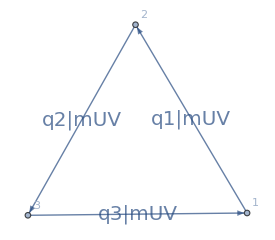
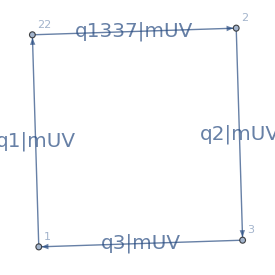
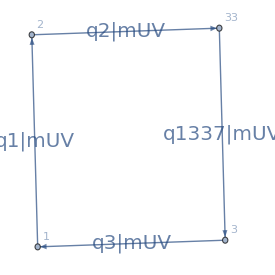
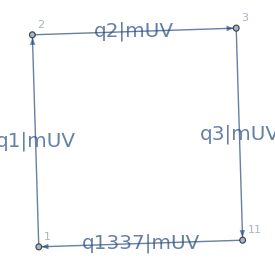
<|{}→-Graphics-,{1}→-Graphics-,{2}→-Graphics-,{3}→-Graphics-|>

```mathematica
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,1,3]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{}->Tri1LUVTopology];
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,22,1],DirectedEdge[2,3,2],DirectedEdge[3,1,3],DirectedEdge[22,2,1337]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV,1337->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{1}->Tri1LUVTopology];
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,33,2],DirectedEdge[3,1,3],DirectedEdge[33,3,1337]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV,1337->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{2}->Tri1LUVTopology];
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,11,3],DirectedEdge[11,1,1337]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|1->mUV,2->mUV,3->mUV,1337->mUV|>,lmb->{1}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]];
AssociateTo[Tri1LUVTopologies,{3}->Tri1LUVTopology]
```

```mathematica
SubtractionData=<|
"I"-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],
"num"->Tri1Lnumerator,
"graph"->Tri1L
|>,
-1-><|
-1-><||>,0-><||>
|>,
0-><|
0-><||>
|>
|>;
```

```mathematica
ComputeSubtractionTerm[ct_,numerics_]:=Module[{orkey,sortedEdgeIDs},
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[ct["graph"]]}]];
Association[SortBy[Table[
orkey=Table[
orientation["Orientation"][eID],
{eID,sortedEdgeIDs}
];
orkey->
(1/λ)^3 EvalcFF[
ct["graph"],
{orientation},
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
Num->ct["num"],
DEBUG->False]
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]]
```

```mathematica
subtractionNumerics=Join[
Tri1Lnumerics,
{mUV->1,
p[1][0]->(p1E/.Tri1Lnumerics),p[2][0]->(p2E/.Tri1Lnumerics),p[3][0]->(p3E/.Tri1Lnumerics),
p[1]->(p1/.Tri1Lnumerics),p[2]->(p2/.Tri1Lnumerics),p[3]->(p3/.Tri1Lnumerics)
}];
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

### First address dod -1 term

```mathematica
AssociateTo[SubtractionData[-1][-1],{}-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True],
"num"-> SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])},
"graph"->Tri1LUVTopologies[{}]
|>];
```

```mathematica
dodm1Res=ComputeSubtractionTerm[SubtractionData[-1][-1][{}],subtractionNumerics];
```

```mathematica
Module[
{tmpI,tmpCT},
Table[
tmpI=SeriesCoefficient[Series[IRes[o],{λ,0,-1},Assumptions->λ>0],-1];
tmpCT=SeriesCoefficient[Series[dodm1Res[o],{λ,0,-1},Assumptions->λ>0],-1];
{o,tmpI,tmpCT,FullSimplify[tmpI-tmpCT]}
,{o,Keys[IRes]}]
]
```

({-1,-1,1} | 0 | 0 | 0
{-1,1,-1} | (11025 ⅈ (11696486+70499 √14494))/(17476517344 √14494) | (11025 ⅈ (11696486+70499 √14494))/(17476517344 √14494) | 0
{-1,1,1} | -(11025 ⅈ (70499 √14494-11696486))/(17476517344 √14494) | -(11025 ⅈ (70499 √14494-11696486))/(17476517344 √14494) | 0
{1,-1,-1} | (11025 ⅈ (11696486+70499 √14494))/(17476517344 √14494) | (11025 ⅈ (11696486+70499 √14494))/(17476517344 √14494) | 0
{1,-1,1} | -(11025 ⅈ (70499 √14494-11696486))/(17476517344 √14494) | -(11025 ⅈ (70499 √14494-11696486))/(17476517344 √14494) | 0
{1,1,-1} | 0 | 0 | 0)

### First address dod 0 term

```mathematica
dod0Expr=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1]+Tri1L4DExprWithFullLambdaDepDODsplits[0],{λ,0,0}],0]//Expand;
```

Now split the above expression into its various denominator structures

```mathematica
lmbVec=q[cFFGetLMBEdges[Tri1L]⟦1⟧/.{DirectedEdge[_,_,props_]:>props["id"]}];
```

```mathematica
lmbData=GenerateLMBData[Tri1L];
lmbDataLambda=Association[Table[k-><|
"mass"->λ lmbData[k]["mass"],"lmb_decomposition"->Simplify[λ (lmbData[k]["lmb_decomposition"]/.{lmbVec->1/λ lmbVec})]|>,
{k,Keys[lmbData]}]]
```

<|1→<|mass→λ,lmb_decomposition→q(1)|>,2→<|mass→2 λ,lmb_decomposition→q(1)-λ (q(4)+q(6))|>,3→<|mass→3 λ,lmb_decomposition→q(1)-λ q(4)|>,4→<|mass→0,lmb_decomposition→λ q(4)|>,5→<|mass→0,lmb_decomposition→λ q(5)|>,6→<|mass→0,lmb_decomposition→λ q(6)|>|>

```mathematica
dod0NumNoDot=<|
{}->ExpandSP4[(dod0Expr/.{x__*Denom[id_,y__]^-2:>0}/.{Denom[y__]:>1})/.{
x__*Derivative[1][q[ie_]][0]Derivative[0,1][SP4][a_,b_]:>x SP4[a,D[lmbDataLambda[ie]["lmb_decomposition"],λ]],
x__*Derivative[1][q[ie_]][0]Derivative[1,0][SP4][a_,b_]:>x SP4[D[lmbDataLambda[ie]["lmb_decomposition"],λ],b]
}/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}]
|>
```

<|{}→-SP4(q(1),q(4)) SP4(q(3),q(4))-SP4(q(1),q(6)) SP4(q(3),q(4))-SP4(q(1),q(2)) SP4(q(4),q(4))|>

```mathematica
dod0NumNoDot[{}]
```

-SP4(q(1),q(4)) SP4(q(3),q(4))-SP4(q(1),q(6)) SP4(q(3),q(4))-SP4(q(1),q(2)) SP4(q(4),q(4))

```mathematica
AssociateTo[SubtractionData[0][0],{}-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[{}],ConvertToNormalisedFormat->True],
"num"-> dod0NumNoDot[{}]/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])},
"graph"->Tri1LUVTopologies[{}]
|>];
```

Now select each dotted topology separately

```mathematica
dod0NumDotted=Association[Table[
{{dot}->(
ExpandSP4[dod0Expr
/.{x__*Power[Denom[idA_,__],-1]*Power[Denom[idB_,__],-1]*Power[Denom[idC_,__],-1]:>0}
/.{x__*Power[Denom[idA_,__],-1]*Power[Denom[idB_,__],-1]*Power[Denom[idC_?(!(#===dot)&),__],-2]:>0}
/.{Denom[y__]:>1}
/.x__ Derivative[1][q[dot]][0]Derivative[0,1][SP4][q[dot][0],q[dot][0]]Derivative[0,1][Denom][dot,z___]:>x SP4[q[1337],D[lmbDataLambda[dot]["lmb_decomposition"],λ]]
/.x__ Derivative[1][q[dot]][0]Derivative[1,0][SP4][q[dot][0],q[dot][0]]Derivative[0,1][Denom][dot,z___]:>x SP4[q[1337],D[lmbDataLambda[dot]["lmb_decomposition"],λ]]
/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}
]
)},
{dot,{1,2,3}}
]]
```

<|{1}→0,{2}→2 SP4(q(1),q(2)) SP4(q(3),q(4)) SP4(q(4),q(1337))+2 SP4(q(1),q(2)) SP4(q(3),q(4)) SP4(q(6),q(1337)),{3}→2 SP4(q(1),q(2)) SP4(q(3),q(4)) SP4(q(4),q(1337))|>

```mathematica
Table[
(*If[!(dod0NumDotted[d]===0),*)
AssociateTo[SubtractionData[0][0],d-><|
"cFFexpr"->CrossFreeFamilyLTD[Tri1LUVTopologies[d],ConvertToNormalisedFormat->True],
"num"-> dod0NumDotted[d]/.{q[a_][0]:>q[a]}/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])},
"graph"->Tri1LUVTopologies[d]
|>];
(*];*)
,{d,Keys[dod0NumDotted]}];
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

```mathematica
dodm0NotDotRes=ComputeSubtractionTerm[SubtractionData[0][0][{}],subtractionNumerics];
```

```mathematica
dodm0DottedRes={
ComputeSubtractionTerm[SubtractionData[0][0][{1}],subtractionNumerics],
ComputeSubtractionTerm[SubtractionData[0][0][{2}],subtractionNumerics],
ComputeSubtractionTerm[SubtractionData[0][0][{3}],subtractionNumerics]
};
```

```mathematica
Module[
{tmpI,tmpCTnoDot,
tmpCTDot1Minus,tmpCTDot2Minus,tmpCTDot3Minus,
tmpCTDot1Plus,tmpCTDot2Plus,tmpCTDot3Plus,
,res,minusKey,plusKey},
res=Table[
tmpI=SeriesCoefficient[Series[IRes[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTnoDot=SeriesCoefficient[Series[dodm0NotDotRes[o],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
minusKey=Join[o,{-1}];
tmpCTDot1Minus=SeriesCoefficient[Series[dodm0DottedRes⟦1⟧[minusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot2Minus=SeriesCoefficient[Series[dodm0DottedRes⟦2⟧[minusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot3Minus=SeriesCoefficient[Series[dodm0DottedRes⟦3⟧[minusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
plusKey=Join[o,{1}];
tmpCTDot1Plus=SeriesCoefficient[Series[dodm0DottedRes⟦1⟧[plusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot2Plus=SeriesCoefficient[Series[dodm0DottedRes⟦2⟧[plusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
tmpCTDot3Plus=SeriesCoefficient[Series[dodm0DottedRes⟦3⟧[plusKey],{λ,0,0},Assumptions->λ>0],0]/.{Missing[x__]:>0};
{o,
tmpI,
(-tmpCTnoDot-tmpCTDot1Minus-tmpCTDot2Minus-tmpCTDot3Minus-tmpCTDot1Plus-tmpCTDot2Plus-tmpCTDot3Plus),
FullSimplify[tmpI-tmpCTnoDot-tmpCTDot1Minus-tmpCTDot2Minus-tmpCTDot3Minus-tmpCTDot1Plus-tmpCTDot2Plus-tmpCTDot3Plus],
tmpCTnoDot,
tmpCTDot1Minus,tmpCTDot1Plus,tmpCTDot2Minus,tmpCTDot2Plus,tmpCTDot3Minus,tmpCTDot3Plus
}
,{o,Keys[IRes]}
];
res=Join[{{
"orientation","I","-SumCT","I-SumCT","CTNoDot","CTDot1-","CTDot1+","CTDot2-","CTDot2+","CTDot3-","CTDot3+"
}},res];
AppendTo[res,Join[{"TOTAL"},
N[Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]]
]]
]//N
```

(orientation | I | -SumCT | I-SumCT | CTNoDot | CTDot1- | CTDot1+ | CTDot2- | CTDot2+ | CTDot3- | CTDot3+
{-1.,-1.,1.} | 0. | 0.-0.0167513 ⅈ | 0.-0.0167513 ⅈ | 0.+0.0167513 ⅈ | 0. | 0. | 0. | 0. | 0. | 0.
{-1.,1.,-1.} | 0.+0.0446379 ⅈ | 0.-0.0446379 ⅈ | 0. | 0.+0.0709223 ⅈ | 0. | 0. | 0.-0.105361 ⅈ | 0.-0.0561538 ⅈ | 0.+0.102604 ⅈ | 0.+0.0326261 ⅈ
{-1.,1.,1.} | 0.-0.00368299 ⅈ | 0.+0.0204343 ⅈ | 0.+0.0167513 ⅈ | 0.-0.0176874 ⅈ | 0. | 0. | 0.-0.0335027 ⅈ | 0.-0.00446394 ⅈ | 0.+0.0326261 ⅈ | 0.+0.00259361 ⅈ
{1.,-1.,-1.} | 0.-0.00456941 ⅈ | 0.+0.0326463 ⅈ | 0.+0.0280769 ⅈ | 0.-0.00636182 ⅈ | 0. | 0. | 0.-0.105361 ⅈ | 0.-0.0561538 ⅈ | 0.+0.102604 ⅈ | 0.+0.0326261 ⅈ
{1.,-1.,1.} | 0.-0.0327217 ⅈ | 0.+0.0327217 ⅈ | 0. | 0.-0.0299748 ⅈ | 0. | 0. | 0.-0.0335027 ⅈ | 0.-0.00446394 ⅈ | 0.+0.0326261 ⅈ | 0.+0.00259361 ⅈ
{1.,1.,-1.} | 0. | 0.-0.0280769 ⅈ | 0.-0.0280769 ⅈ | 0.+0.0280769 ⅈ | 0. | 0. | 0. | 0. | 0. | 0.
TOTAL | 0.+0.00366375 ⅈ | 0.-0.00366375 ⅈ | 0.+0. ⅈ | 0.+0.0617266 ⅈ | 0. | 0. | 0.-0.277727 ⅈ | 0.-0.121235 ⅈ | 0.+0.270461 ⅈ | 0.+0.0704393 ⅈ)